```mathematica
gam=Gamma[1/4]^2/(32 Pi)^(1/2);
g[x_]:= x/(1 + x^2)^(5/4);
{c1,c2,c3,c4}={0.17467008438086054,3.2237984506125503,2.224790597667039,1.8906775733050594};
h[x_]:=1/gam(1 - c1 x^2)/(1 +c2 x^2 + c3 x^4 + c4 x^6 + (c1/gam)^(16/7)x^8)^(7/16);
```

```mathematica
ifxc[y_]:=NIntegrate[(y h[x] + x g[x])/(x^2 + y^2),{x,0,Infinity}]gam/(Pi)
```

```mathematica
Integrate[ g[x]/x,{x,-Infinity,Infinity},PrincipalValue->True] gam/(Pi)//FullSimplify
```

1

```mathematica
dat=Import["/Users/aaronkaplan/Dropbox/phd.nosync/mcp07_revised/code/test_fits/gki_fxc_ifreq.csv","Data"];
{w,fxcu} = Transpose[Table[{dat[[i,1]],dat[[i,2]]},{i,2,Length[dat]}]];
```

```mathematica
fxcum = Table[ifxc[w[[i]]],{i,1,Length[w]}];
```

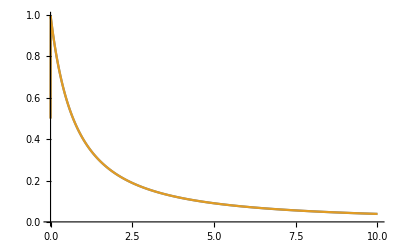

```mathematica
ListPlot[{Transpose[{w,fxcu}],Transpose[{w,fxcum}]},Joined->True,PlotRange->Full]
```

```mathematica
t[x_,a_,b_,c_,d_,f_]:=(1 - a x+b x^2)/(1 +c x^2 +d x^4+ f x^6 +(b/gam)^(16/7) x^8)^(7/16)
```

```mathematica
Manipulate[Show[{ListPlot[Transpose[{w,fxcu}],Joined->True,PlotRange->Full],Plot[t[x,1.2245917427436879,0.9781163969819368,0.39584293028797224,1.3301909351895291,1.0061444008856923],{x,w[[2]],w[[Length[w]]]},PlotStyle->Orange,PlotRange->Full]}],{a,.01,2},{b,0.01,2},{c,0.01,2},{d,0.01,2}]
```